```mathematica
ClearAll["Global`*"]
```

## Calculating the elliptic potential V(q) using the Jacobi Amplitude of module m

## The module in amu(q,k) is taken as k^2=m (as per the default behavior of the Wolfram implementation) -Graphics-

```mathematica
prepath="/Users/basavyr/Documents/Work/Repos/mathematica-useful-algorithms/Physics/Elliptic-Functions-New-Boson/Figures";
export[object_, name_, format_]:=Export[StringTemplate["``/``.``"][prepath,name, format],object, ImageResolution->1200];
```

```mathematica
fit1MOI={91,9,51};
fit2MOI={13.53,101.76,52.94};
fit3MOI={89,12,48};
thetadegfit1=-119;
thetadegfit2=140;
thetadegfit3=-71;
oddspin=5.5;
A[mois_]:=N[1/(2*#)]&/@mois;
rad[theta_]:=N[theta*π/180];
```

Angular momentum vector j

```mathematica
j1[thetadeg_]:=oddspin*Cos[rad[thetadeg]];
j2[thetadeg_]:=oddspin*Sin[rad[thetadeg]];
```

Pre-Elliptic factors

```mathematica
Aterm[I_,thetadeg_,mois_]:=A[mois][[2]](1-j2[thetadeg]/I)-A[mois][[1]];
uterm[I_,thetadeg_,mois_]:=(A[mois][[3]]-A[mois][[1]])/Aterm[I,thetadeg,mois];
v0term[I_,thetadeg_,mois_]:=-(A[mois][[1]]*j1[thetadeg])/Aterm[I,thetadeg,mois];
kterm[I_,thetadeg_,mois_]:=Sqrt[Abs[uterm[I,thetadeg,mois]]];
```

Elliptic functions

```mathematica
phi[q_,k_]:=JacobiAmplitude[q,k^2];
sn[q_,k_]:=Sin[phi[q,k]];
cn[q_,k_]:=Cos[phi[q,k]];
dn[q_,k_]:=√(1-k^2 sn[q,k]^2);
```

Period for the elliptic functions-Graphics-

```mathematica
period[k_]:=NIntegrate[1/(√(1-k^2 Sin[t]^2)),{t,0,π/2}];
```

Elliptic Potential V_I(q)

```mathematica
Vq[q_,I_,thetadeg_,mois_]:=(I*(I+1)*kterm[I,thetadeg,mois]^2+v0term[I,thetadeg,mois]^2)*sn[q,kterm[I,thetadeg,mois]]^2+(2I+1)*v0term[I,thetadeg,mois]*cn[q,kterm[I,thetadeg,mois]]*dn[q,kterm[I,thetadeg,mois]];
```

Helper tools

```mathematica
linspace[a_,b_,n_]:=Table[N[i],{i,a,b,(b-a)/(n-1)}];
```

Tabulated values (tests)

```mathematica
(* Test values for the total angular momentum and the modulus k *)
spinvalues={22.5,18.5,14.5};
qrange[thetadeg_,mois_]:=Max[Table[4*period[kterm[spin,thetadeg,mois]],{spin,spinvalues}]];
(* Tabulated values with the Elliptic values*)
qvalues[thetadeg_,mois_]:=linspace[-qrange[thetadeg,mois],qrange[thetadeg,mois],300];
(*phivalues=Table[SetPrecision[phi[qvalues[[i]],ktest],4],{i, 1, Length[qvalues]}];*)
(*snvalues=Table[SetPrecision[sn[qvalues[[i]],ktest],4],{i, 1, Length[qvalues]}];*)
(*cnvalues=Table[SetPrecision[cn[qvalues[[i]],ktest],4],{i, 1, Length[qvalues]}];*)
(*dnvalues=Table[SetPrecision[dn[qvalues[[i]],ktest],4],{i, 1, Length[qvalues]}];*)
(*vqvalues=Table[Vq[qvalues[[i]],Itest],{i, 1, Length[qvalues]}];*)
(*export[TableView[Table[{qvalues[[i]],ktest,phivalues[[i]],snvalues[[i]],cnvalues[[i]],dnvalues[[i]],vqvalues[[i]]},{i,1,Length[qvalues]}],Headers->{{"q","k","φ(q,k)","sn(q,k)", "cn(q,k)", "dn(q,k)","V_I(q)"},Automatic}],"elliptic-data","csv"];*)
```

## Fitting parameters 𝒫_fit^1

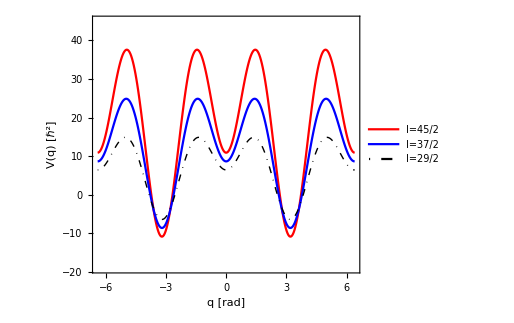

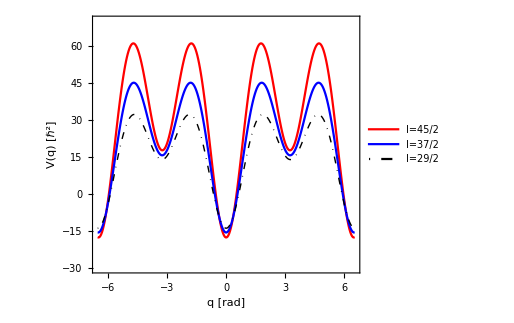

```mathematica
fit1Plot1[spinvalues_]:=ListLinePlot[Table[Table[{q,Vq[q,spin,thetadegfit1,fit1MOI]},{q,qvalues[thetadegfit1,fit1MOI]}],{spin,spinvalues}],
Frame->True,
Axes->False,
FrameLabel->{"q [rad]","V(q) [ℏ^2]"},
AspectRatio->0.85,
FrameStyle->Directive[Black,Thick],
PlotStyle->{{Red},{Blue},{Black,Thick,DotDashed}},
LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},
ImageSize->380,
PlotLegends->Placed[Table[Style[StringTemplate["I=``/2"][Round[2*spin]],16],{spin,spinvalues}],{0.5,0.2}],
PlotRange->{-19,45}
];
fit1Plot2[spinvalues_]:=ListLinePlot[Table[Table[{q,Vq[q,spin,thetadegfit1+180,fit1MOI]},{q,qvalues[thetadegfit1+180,fit1MOI]}],{spin,spinvalues}],
Frame->True,
Axes->False,
FrameLabel->{"q [rad]","V(q) [ℏ^2]"},
AspectRatio->0.85,
FrameStyle->Directive[Black,Thick],
PlotStyle->{{Red},{Blue},{Black,Thick,DotDashed}},
LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},
ImageSize->380,
PlotLegends->Placed[Table[Style[StringTemplate["I=``/2"][Round[2*spin]],16],{spin,spinvalues}],{0.25,0.2}],
PlotRange->{-30,70}
];
Show[fit1Plot1[spinvalues]]
Show[fit1Plot2[spinvalues]]
export[Show[fit1Plot1[spinvalues]],"potential-fit-theta","pdf"];
export[Show[fit1Plot2[spinvalues]],"potential-fit-theta-pi","pdf"];
```

## Fitting parameters 𝒫_fit^2

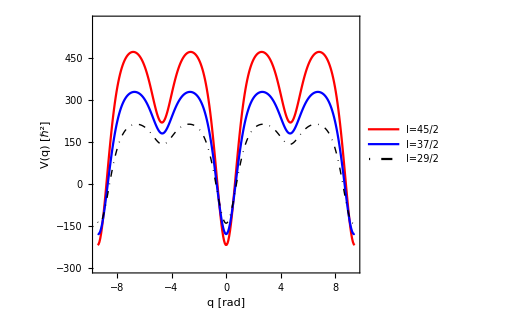

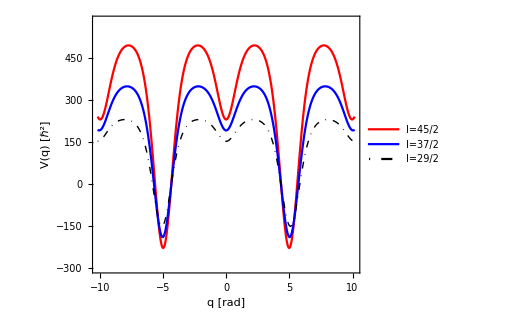

```mathematica
fit2Plot1[spinvalues_]:=ListLinePlot[Table[Table[{q,Vq[q,spin,thetadegfit2,fit2MOI]},{q,qvalues[thetadegfit2,fit2MOI]}],{spin,spinvalues}],
Frame->True,
Axes->False,
FrameLabel->{"q [rad]","V(q) [ℏ^2]"},
AspectRatio->0.85,
FrameStyle->Directive[Black,Thick],
PlotStyle->{{Red},{Blue},{Black,Thick,DotDashed}},
LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},
ImageSize->380,
PlotLegends->Placed[Table[Style[StringTemplate["I=``/2"][Round[2*spin]],16],{spin,spinvalues}],{0.26,0.2}],
PlotRange->{-300,580}
];
fit2Plot2[spinvalues_]:=ListLinePlot[Table[Table[{q,Vq[q,spin,thetadegfit2+180,fit2MOI]},{q,qvalues[thetadegfit2+180,fit2MOI]}],{spin,spinvalues}],
Frame->True,
Axes->False,
FrameLabel->{"q [rad]","V(q) [ℏ^2]"},
AspectRatio->0.85,
FrameStyle->Directive[Black,Thick],
PlotStyle->{{Red},{Blue},{Black,Thick,DotDashed}},
LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},
ImageSize->380,
PlotLegends->Placed[Table[Style[StringTemplate["I=``/2"][Round[2*spin]],16],{spin,spinvalues}],{0.5,0.2}],
PlotRange->{-300,580}
];
Show[fit2Plot1[spinvalues]]
Show[fit2Plot2[spinvalues]]
export[Show[fit2Plot1[spinvalues]],"potential-fit2-theta","pdf"];
export[Show[fit2Plot2[spinvalues]],"potential-fit2-theta-pi","pdf"];
```